```mathematica
Bisection[f_,a0_,b0_,err0_, value_]:= Module[{a,b,c,i, current, v1, err},
a = a0;
b = b0;
c = (a + b) / 2;
i = 0;
v1 = value;
current = N[Abs[(c-v1)/v1]] * 100;
err = err0;
While[i< 100,
If[f[a]  *f[c] > 0,
a= c, b = c];
c = (a + b) / 2;
current = N[Abs[(c-v1)/v1]] * 100;
i = i + 1;
];
Return[N[c], Module];
];
sigma = 0.6;
W = 16000;
d[v_] := 0.01 * sigma * v ^ 2 + 0.95 / sigma * (W/v)^2
```

```mathematica
g:=D[d[v], v]
```

```mathematica
g
```

-(8.10667×10^8)/v^3+0.012 v

```mathematica
s = NSolve[g==0, v, Reals]
d'[10]
```

{}

-810667.

```mathematica
v/.s
```

{509.818,-509.818}

```mathematica
b = Bisection[d', 400, 600, 0.1, 509]
```

509.818

```mathematica
b
```

1027/2

```mathematica
v1 = 509.8181203738957;
```

```mathematica
d[v1]
```

3118.97

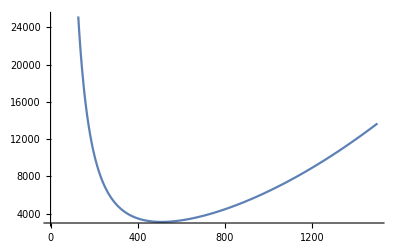

```mathematica
Plot[d[v], {v, 0, 1500}]
```

```mathematica
Manipulate[Plot[0.01 * sigma * v^ 2 + 0.95 / sigma * (w/v)^2, {v, 0, 1500}], {w, 12000, 20000, 10}]
```

```mathematica
W=12000;
sigma = 0.6;
vs = {};
raports = {};
ds = {};
While[W<20000,
d[v_] := 0.01 * sigma * v ^ 2 + 0.95 / sigma * (W/v)^2;
g:=D[d[v], v];
W = W + 100;
s = NSolve[g==0, v, Reals];
t = v/.s[[1]] ;
t2 = v /.s[[2]];
b = Bisection[d', 400, 600, 0.1, t];
AppendTo[vs,b]; AppendTo[raports, b / d[b]];AppendTo[ds,d[b]];
]
```

```mathematica
raports
```

{0.187962,0.18719,0.186428,0.185675,0.18493,0.184195,0.183469,0.18275,0.182041,0.181339,0.180646,0.17996,0.179282,0.178612,0.177949,0.177294,0.176646,0.176005,0.17537,0.174743,0.174122,0.173508,0.1729,0.172299,0.171704,0.171115,0.170532,0.169954,0.169383,0.168818,0.168258,0.167703,0.167154,0.166611,0.166072,0.165539,0.165011,0.164488,0.16397,0.163457,0.162949,0.162445,0.161946,0.161451,0.160961,0.160476,0.159995,0.159518,0.159045,0.158577,0.158112,0.157652,0.157196,0.156743,0.156295,0.15585,0.155409,0.154972,0.154539,0.154109,0.153682,0.15326,0.15284,0.152424,0.152012,0.151603,0.151197,0.150794,0.150395,0.149998,0.149605,0.149215,0.148828,0.148444,0.148063,0.147685,0.147309,0.146937,0.146567,0.1462}

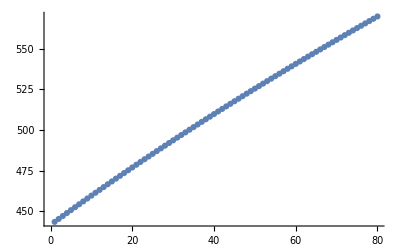

```mathematica
ListPlot[vs]
```

```mathematica
ListPlot[vs, raports]
```

ListPlot::nonopt: Options expected (instead of {0.187962,0.18719,0.186428,0.185675,0.18493,0.184195,0.183469,0.18275,0.182041,«34»,0.161451,0.160961,0.160476,0.159995,0.159518,0.159045,0.158577,«30»}) beyond position 1 in ListPlot[{443.351,445.18,447.,448.814,450.62,452.419,454.21,455.995,457.773,«34»,516.152,517.723,519.289,520.851,522.408,523.961,525.508,«30»},{«1»}]. An option must be a rule or a list of rules.

ListPlot[{443.351,445.18,447.,448.814,450.62,452.419,454.21,455.995,457.773,459.544,461.308,463.065,464.816,466.56,468.298,470.029,471.754,473.473,475.185,476.891,478.591,480.285,481.974,483.656,485.332,487.003,488.668,490.327,491.981,493.629,495.272,496.909,498.541,500.168,501.789,503.405,505.016,506.622,508.222,509.818,511.409,512.995,514.575,516.152,517.723,519.289,520.851,522.408,523.961,525.508,527.052,528.591,530.125,531.655,533.181,534.702,536.219,537.731,539.24,540.744,542.244,543.74,545.231,546.719,548.203,549.682,551.158,552.63,554.097,555.561,557.022,558.478,559.93,561.379,562.824,564.265,565.703,567.137,568.567,569.994},{0.187962,0.18719,0.186428,0.185675,0.18493,0.184195,0.183469,0.18275,0.182041,0.181339,0.180646,0.17996,0.179282,0.178612,0.177949,0.177294,0.176646,0.176005,0.17537,0.174743,0.174122,0.173508,0.1729,0.172299,0.171704,0.171115,0.170532,0.169954,0.169383,0.168818,0.168258,0.167703,0.167154,0.166611,0.166072,0.165539,0.165011,0.164488,0.16397,0.163457,0.162949,0.162445,0.161946,0.161451,0.160961,0.160476,0.159995,0.159518,0.159045,0.158577,0.158112,0.157652,0.157196,0.156743,0.156295,0.15585,0.155409,0.154972,0.154539,0.154109,0.153682,0.15326,0.15284,0.152424,0.152012,0.151603,0.151197,0.150794,0.150395,0.149998,0.149605,0.149215,0.148828,0.148444,0.148063,0.147685,0.147309,0.146937,0.146567,0.1462}]

```mathematica
data=Transpose@{vs,ds};
```

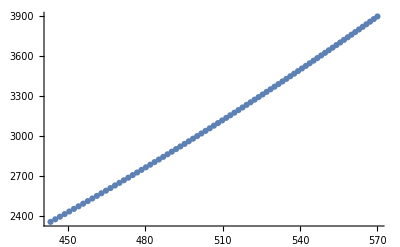

```mathematica
ListPlot[data]
```